## 常微分方程

最基本的范例入手-Airy Function

```mathematica
DSolve[{y''[x]-x*y[x]==0},y,x]
```

{{y→Function[{x},AiryAi[x] C[1]+AiryBi[x] C[2]]}}

加入初始条件

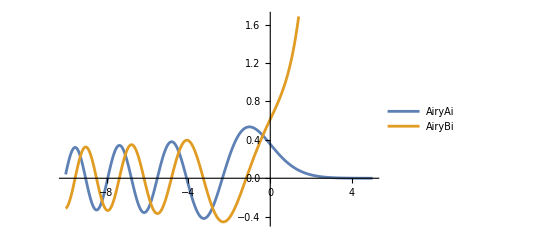

```mathematica
sol=DSolve[{y''[x]-x*y[x]==0},y,x]//Quiet;
Plot[Evaluate[y[x]/.%/.{{C[1]->1,C[2]->0},{C[1]->0,C[2]->1}}],
{x,-10,5},
PlotLegends->{"AiryAi","AiryBi"}
]
```

受迫振动

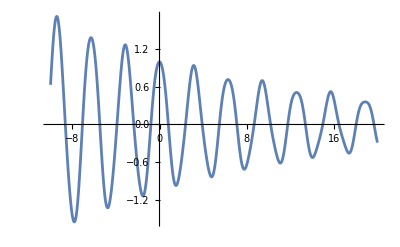

```mathematica
sol=DSolve[{x''[t]+γ x'[t]+ω^2 x[t]==A Cos[o t],x'[0]==0,x[0]==1},x,t]/.{γ->0.1,ω->2,A->1,o->5};

Plot[Evaluate[x[t]/.sol],{t,-10,20}]
```

```mathematica
eqn={y'[x]==y[x]^2,y[0]==1};
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},1/(1-x)]}}

微分方程组

{{x[t]→(-1+2 t+2 ArcTan[t]+t Log[1+t^2])/(2 (1+t^2)),y[t]→(4+t+2 t^2-2 t ArcTan[t]+Log[1+t^2])/(2 (1+t^2))}}

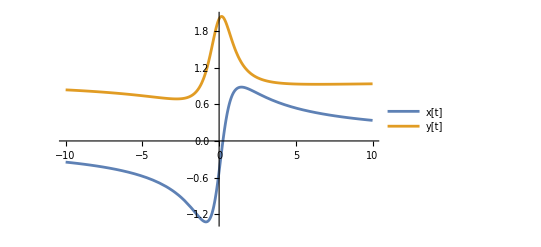

```mathematica
eqns={(t^2+1)*x'[t]==-t*x[t]+y[t],(t^2+1)*y'[t]==-x[t]-t*y[t]+t,x[0]==-1/2,y[0]==2};
sol=DSolve[eqns,{x[t],y[t]},t]
Plot[{x[t]/. sol,y[t]/. sol},{t,-10,10},PlotLegends->{"x[t]","y[t]"}]
```

偏微分方程

```mathematica
eqn=x^2*D[u[x,y],x]+y^2*D[u[x,y],y]-(x+y)*u[x,y];
sol=DSolve[eqn==0,u,{x,y}]
fn=u[x,y]/. sol[[1]]/. {C[1][t_]->Exp[-t]}
Plot3D[fn,{x,-5,5},{y,-5,5},PlotStyle->Directive[Opacity[0.8],RGBColor[0.5,0.7,1],Specularity[White,40]]]
```

{{u→Function[{x,y},x y C[1][1/x-1/y]]}}

ⅇ^(-1/x+1/y) x y

-Graphics3D-

一维杆子上的热传导

```mathematica
Clear["Global`*"]  
eqn=0.1*D[u[x,t],{x,2}]-D[u[x,t],t]==0;
sol=DSolve[{eqn,{u[0,t]==0,u[10,t]==10},u[x,0]==20},u,{x,t}]
```

{{u→Function[{x,t},x+-(20 (-2+(-1)^K[1]) ⅇ^(-0.0098696 t K[1]^2) Sin[1/10 π x K[1]])/(π K[1])K[1]1∞]}}

```mathematica
approxsol=TruncateSum[u[x,t]/. sol[[1]],100]//Expand;
Plot3D[approxsol,{x,0,10},{t,0,300},PlotStyle->Directive[Opacity[0.8],RGBColor[0.5,0.7,1],Specularity[White,10]],AxesLabel->{"x","t","u[x,t]"}]
```

-Graphics3D-

```mathematica
sol=DSolve[{x'[t]+t*y[t]==0,2 y'[t]-3 x[t]==0,x[0]==1,y[0]==3},{x,y},t]
```

技术笔记参考：
-Graphics-
https://reference.wolfram.com/language/tutorial/DSolveOverview.html

数值求解介绍：
-Graphics-
https://reference.wolfram.com/language/tutorial/NumericalOperationsOnFunctions.html#17230

a'[t]==√(0.7+1/(20000 a[t]^4)+0.3/a[t]^3) a[t]

NDSolve::ndsz: 在 t == -0.963865 处，步长实际上为零；可能存在奇点或者刚性系统.

{{a[t]→InterpolatingFunction[…][t]}}

InterpolatingFunction::dmval: 输入值 {-0.999918} 位于插值函数的数据范围之外. 将使用外推法.

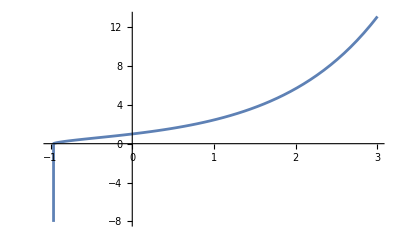

```mathematica
Clear["Global`*"]  
eqa=a'[t]==a[t]*(0.3*a[t]^-3+5*10^-5*a[t]^-4+0.7)^(1/2)
NDSolve[{eqa,a[0]==1},a[t],{t,-1,3}]
Plot[a[t]/.%,{t,-1,3}]
```

{{y→InterpolatingFunction[…]}}

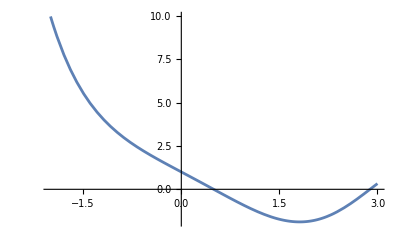

```mathematica
Clear["Global`*"]  
NDSolve[{y''[x]+x y[x]==0,y[0]==1,y[1]==-1},y,{x,-3,3}]
Plot[Evaluate[y[x]/.%],{x,-2,3}]
```

数值求解引力轨道

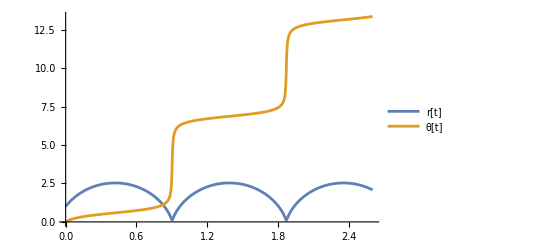

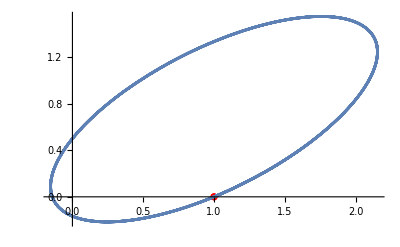

```mathematica
α=100;
H=5;
sol=NDSolve[{r''[t]-r [t] θ'[t]^2==-α/r[t]^2,θ'[t]==H/r[t]^2,θ[0]==0,r[0]==1,r'[0]==10},{r,θ},{t,0,5}];
Plot[Evaluate[{r[t],θ[t]}/. sol],{t,0,2.6},WorkingPrecision->50,PlotLegends->{"r[t]","θ[t]"}]

Show[ListPlot[Evaluate[{r[t] Cos[θ[t]],r[t] Sin[θ[t]]}/. sol]/.t->0,PlotStyle->Red],
ParametricPlot[Evaluate[{r[t] Cos[θ[t]],r[t] Sin[θ[t]]}/. sol],{t,0,4}],
PlotRange->All
]
```

```mathematica
NDSolve[{x'[t]==-3 (x[t]-y[t]),y'[t]==-x[t] z[t]+26.5 x[t]-y[t],z'[t]==x[t] y[t]-z[t],x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,200},MaxSteps->Infinity]
Manipulate[ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. %],{t,0,T},PlotPoints->10000,ColorFunction->(ColorData["Rainbow"][#4]&)],{T,0.1,200}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}